## Author Informations

#### Authors: A. C. Lehum, Huan Souza Date: 18/05/2021 Filiation: Universidade Federal do Pará Emails: lehum@ufpa.br, huan.souza@icen.ufpa.br

# Electrodynamics coupled to linearized gravity

#### Preliminaries

```mathematica
Quit[]
```

```mathematica
description="Electrodynamics coupled to linearized gravity";
If[$FrontEnd===Null,$FeynCalcStartupMessages=False;
Print[description];];
If[$Notebooks===False,$FeynCalcStartupMessages=False];
$LoadAddOns={"FeynArts","FeynHelpers"};
Get["FeynCalc`"]
$FAVerbose=0;
FCCheckVersion[9,3,0];
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (3 Aug 2020) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
FAPatch[PatchModelsOnly->True];
$KeepLogDivergentScalelessIntegrals=True;
MakeBoxes[mu,TraditionalForm]:="μ";
MakeBoxes[nu,TraditionalForm]:="ν";
MakeBoxes[p1,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(1\)]\)";
MakeBoxes[p2,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(2\)]\)";
MakeBoxes[p3,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(3\)]\)";
MakeBoxes[p4,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(4\)]\)";
MakeBoxes[k1,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(1\)]\)";
MakeBoxes[k2,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(2\)]\)";
MakeBoxes[k3,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(3\)]\)";
MakeBoxes[k4,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(4\)]\)";
MakeBoxes[m1,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), \(1\)]\)";
MakeBoxes[m2,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), \(2\)]\)";
ScalarProduct[p,p]=p^2
```

p^2

#### 1-loop γ self-energy

In this section, we compute the photon wave-function counterterm at one-loop order.

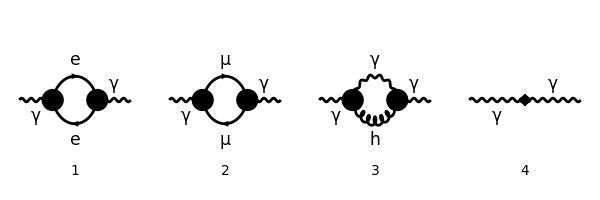

```mathematica
fields1={InsertionLevel->{Classes},GenericModel->FileNameJoin[{"Einstein_QED_2","Einstein_QED_2"}],Model->FileNameJoin[{"Einstein_QED_2","Einstein_QED_2"}]};
top1[i_,j_]:=CreateTopologies[1,i->j,ExcludeTopologies->{Reducible},Adjacencies->{3,4,5}];
top1CT[i_,j_]:=CreateCTTopologies[1,i->j,ExcludeTopologies->{Reducible},Adjacencies->{3,4,5}];
{phSE1,phSE1CT}=(InsertFields[#1,{V[1]}->{V[1]},Sequence@@fields1]&)/@{top1[1,1],top1CT[1,1]};
diag1[0]=phSE1[[0]][Sequence@@phSE1,Sequence@@phSE1CT];
Paint[diag1[0],ColumnsXRows->{4,1},SheetHeader->{"Photon self-energy"},Numbering->Simple,ImageSize->{600,200}];
```

```mathematica
AbsoluteTiming[For[
i=1,i≤4,i++,{
amp[i]=DiagramExtract[diag1[0],i],
amp1[i]=FCFAConvert[CreateFeynAmp[amp[i],Truncated->True,PreFactor->1,GaugeRules->{}],IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{k},List->False,SMP->True,ChangeDimension->D,LorentzIndexNames->{mu,nu,α,γ,δ,β,ξ,χ},UndoChiralSplittings->True,Contract->True,FinalSubstitutions->{Z3->1+δ3}]//Simplify,
amp2[i]=DiracSimplify[TID[amp1[i],k,ToPaVe->True,UsePaVeBasis->True]],
amp3[i]=SelectNotFree2[Normal[Series[FCReplaceD[PaVeUVPart[amp2[i],Prefactor->1/(2*π)^D],D->4-2*Epsilon],{Epsilon,0,0}]],{Epsilon,δ3}]}
];]
```

{4.44344,Null}

```mathematica
photon[1]=Sum[amp3[i],{i,1,4}]
```

-(ⅈ e^2 (p^2 g^μν-p^μ p^ν))/(6 π^2 ε)-ⅈ δ3 (p^2 g^μν-p^μ p^ν)-(ⅈ (-2 κ^2 p^4 g^μν+3 κ^2 p^4 ξ_(T(1)) g^μν+2 κ^2 p^2 p^μ p^ν-3 κ^2 p^2 p^μ p^ν ξ_(T(1))))/(96 π^2 ε)

```mathematica
photon[2]=SelectNotFree2[Collect2[photon[1],{"κ"},Factoring->Simplify],{Epsilon,δ3}]
```

-(ⅈ e^2 (p^2 g^μν-p^μ p^ν))/(6 π^2 ε)-ⅈ δ3 (p^2 g^μν-p^μ p^ν)-(ⅈ κ^2 p^2 (3 ξ_(T(1))-2) (p^2 g^μν-p^μ p^ν))/(96 π^2 ε)

```mathematica
photon[3]=Coefficient[photon[2],(p^2 Pair[LorentzIndex[mu,D],LorentzIndex[nu,D]]-Pair[LorentzIndex[mu,D],Momentum[p,D]] Pair[LorentzIndex[nu,D],Momentum[p,D]])]
```

-ⅈ δ3-(ⅈ e^2)/(6 π^2 ε)-(ⅈ κ^2 p^2 (3 ξ_(T(1))-2))/(96 π^2 ε)

Now, we take only the terms proportional to p⁰, the term proportional to p.b2 will be renormalized by a higher-order operator.

```mathematica
Solve[SelectFree2[photon[3],p]==0,δ3]
```

{{δ3→-e^2/(6 π^2 ε)}}

#### 1-loop electron self-energy

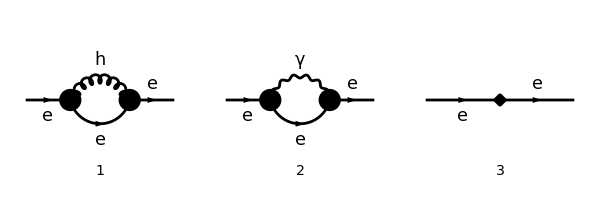

```mathematica
fields1={InsertionLevel->{Classes},GenericModel->FileNameJoin[{"Einstein_QED_2","Einstein_QED_2"}],Model->FileNameJoin[{"Einstein_QED_2","Einstein_QED_2"}]};
top1[i_,j_]:=CreateTopologies[1,i->j,ExcludeTopologies->{Reducible},Adjacencies->{3,4,5}];
top1CT[i_,j_]:=CreateCTTopologies[1,i->j,ExcludeTopologies->{Reducible},Adjacencies->{3,4,5}];
{sepsi1,sepsi1CT}=(InsertFields[#1,{F[1]}->{F[1]},Sequence@@fields1]&)/@{top1[1,1],top1CT[1,1]};
diag2[0]=sepsi1[[0]][Sequence@@sepsi1,Sequence@@sepsi1CT];
Paint[diag2[0],ColumnsXRows->{3,1},SheetHeader->{"Electron self-energy"},Numbering->Simple,ImageSize->{600,200}];
```

```mathematica
AbsoluteTiming[For[
i=1,i≤3,i++,{
Famp[i]=DiagramExtract[diag2[0],i],
Famp1[i]=FCFAConvert[CreateFeynAmp[Famp[i],Truncated->True,PreFactor->1,GaugeRules->{}],IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{k},List->False,SMP->True,ChangeDimension->D,LorentzIndexNames->{mu,nu,α,γ,δ,β,ξ,χ},UndoChiralSplittings->True,Contract->True,FinalSubstitutions->{Z2->1+δ2,Zm->1+δm,Z9->1+δ9,Z8->1+δ8}]//Simplify,
Famp2[i]=DiracSimplify[TID[Famp1[i],k,ToPaVe->True,UsePaVeBasis->True]],
Famp3[i]=SelectNotFree2[Normal[Series[FCReplaceD[PaVeUVPart[Famp2[i],Prefactor->1/(2*π)^D],D->4-2*Epsilon],{Epsilon,0,0}]],{Epsilon,δ2,δm,δ9,δ8}]}
];]
```

{6.66697,Null}

```mathematica
fermion[1]=Sum[Famp3[i],{i,1,3}]//DotExpand//Simplify//Expand//Factor
```

-1/(512 π^2 ε)(-32 ⅈ e^2 ξ_(V(1)) γ·p+32 ⅈ e^2 m_1 ξ_(V(1))+96 ⅈ e^2 m_1+512 ⅈ π^2 δ8 ε e1 p^2 γ·p+512 π^2 δ9 ε e2 p^2 m_1+19 ⅈ κ^2 p^2 γ·p-36 ⅈ κ^2 p^2 m_1+24 ⅈ κ^2 p^2 m_1 ξ_(T(1))-15 ⅈ κ^2 p^2 ξ_(T(1)) γ·p-512 ⅈ π^2 δ2 ε γ·p-37 ⅈ κ^2 m_1^2 γ·p+29 ⅈ κ^2 m_1^2 ξ_(T(1)) γ·p+46 ⅈ κ^2 m_1^3-38 ⅈ κ^2 m_1^3 ξ_(T(1))+512 ⅈ π^2 δm ε m_1)

```mathematica
fermionHO[1]=SelectNotFree2[fermion[1],p^2]
```

-ⅈ δ8 e1 p^2 γ·p+δ9 (-e2) p^2 m_1-(19 ⅈ κ^2 p^2 γ·p)/(512 π^2 ε)+(9 ⅈ κ^2 p^2 m_1)/(128 π^2 ε)-(3 ⅈ κ^2 p^2 m_1 ξ_(T(1)))/(64 π^2 ε)+(15 ⅈ κ^2 p^2 ξ_(T(1)) γ·p)/(512 π^2 ε)

The divergence fermionHO[1] is absorbed by the high order counterterms δ8 and δ9.

```mathematica
fermionDirac[1]=SelectFree2[fermion[1],p^2]//Simplify//Expand//Simplify
```

-(ⅈ (γ·p (-512 π^2 δ2 ε-32 e^2 ξ_(V(1))-37 κ^2 m_1^2+29 κ^2 m_1^2 ξ_(T(1)))+32 e^2 m_1 ξ_(V(1))+96 e^2 m_1+46 κ^2 m_1^3-38 κ^2 m_1^3 ξ_(T(1))+512 π^2 δm ε m_1))/(512 π^2 ε)

The term fermionDirac[1] is the UV divergent correction to Dirac Lagrangian.  The muon self-energy is obtained by the replacement of F[1]  to F[2] in the sepsi1 function.

```mathematica
Solve[SelectNotFree2[fermionDirac[1],DiracGamma]==0,δ2]//FullSimplify
Solve[SelectFree2[fermionDirac[1],DiracGamma]==0,δm]//Expand
```

{{δ2→(κ^2 m_1^2 (29 ξ_(T(1))-37)-32 e^2 ξ_(V(1)))/(512 π^2 ε)}}

{{δm→-(3 e^2)/(16 π^2 ε)-(e^2 ξ_(V(1)))/(16 π^2 ε)-(23 κ^2 m_1^2)/(256 π^2 ε)+(19 κ^2 m_1^2 ξ_(T(1)))/(256 π^2 ε)}}

#### 1-loop vertex correction

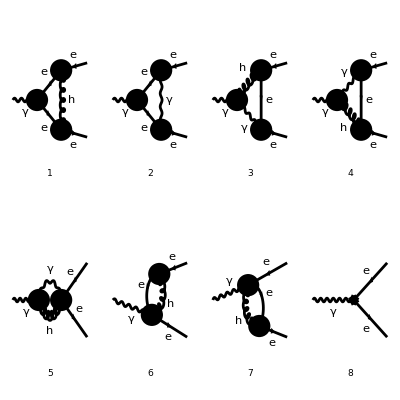

```mathematica
fields1={InsertionLevel->{Classes},GenericModel->FileNameJoin[{"Einstein_QED_2","Einstein_QED_2"}],Model->FileNameJoin[{"Einstein_QED_2","Einstein_QED_2"}]};
top1[i_,j_]:=CreateTopologies[1,i->j,ExcludeTopologies->{Reducible},Adjacencies->{3,4,5}];
top1CT[i_,j_]:=CreateCTTopologies[1,i->j,ExcludeTopologies->{Reducible},Adjacencies->{3,4,5}];
{vertex1,vertex1CT}=(InsertFields[#1,{V[1]}->{-F[1],F[1]},Sequence@@fields1]&)/@{top1[1,2],top1CT[1,2]};
diag3[0]=vertex1[[0]][Sequence@@vertex1,Sequence@@vertex1CT];
Paint[diag3[0],ColumnsXRows->{4,2},SheetHeader->{"Vertex correction"},Numbering->Simple,ImageSize->{400,400}];
```

```mathematica
AbsoluteTiming[For[
i=1,i≤8,i++,{
amp[i]=DiagramExtract[diag3[0],i],
amp1[i]=FCFAConvert[CreateFeynAmp[amp[i],Truncated->True,PreFactor->1,GaugeRules->{}],IncomingMomenta->{p1},OutgoingMomenta->{p2,p3},LoopMomenta->{k},List->False,SMP->True,ChangeDimension->D,LorentzIndexNames->{mu,nu,α,γ,δ,β,ξ,χ},UndoChiralSplittings->True,Contract->True,FinalSubstitutions->{Z1->1+δ1,Z11->1+δ11}]//Simplify,
amp2[i]=DiracSimplify[TID[amp1[i],k,ToPaVe->True,UsePaVeBasis->True]],
amp3[i]=SelectNotFree2[Normal[Series[FCReplaceD[PaVeUVPart[amp2[i],Prefactor->1/(2*π)^D],D->4-2*Epsilon],{Epsilon,0,0}]],{Epsilon,δ1,δ11}]}
];]
```

{319.712,Null}

```mathematica
amp4[0]=Collect2[Sum[amp3[i],{i,1,8}],{δ1,δ11},Factoring->Simplify]
```

δ11 (e4 γ^μ (p_1·p_2)-e4 γ·p_1 p_2^μ)+ⅈ δ1 γ^μ e+1/(12288 ε π^2)ⅈ e ((260 m_1 γ^μ.(γ·p_3)-240 m_1 ξ_(T(1)) γ^μ.(γ·p_3)+432 m_1 (γ·p_1).γ^μ-164 m_1 (γ·p_2).γ^μ+692 m_1 (γ·p_3).γ^μ-160 γ^μ.(γ·p_1).(γ·p_2)-56 γ^μ.(γ·p_1).(γ·p_3)-80 γ^μ.(γ·p_2).(γ·p_1)-83 γ^μ.(γ·p_2).(γ·p_3)-112 γ^μ.(γ·p_3).(γ·p_1)+81 γ^μ.(γ·p_3).(γ·p_2)+160 (γ·p_1).γ^μ.(γ·p_2)+56 (γ·p_1).γ^μ.(γ·p_3)+80 (γ·p_1).(γ·p_2).γ^μ+112 (γ·p_1).(γ·p_3).γ^μ-40 (γ·p_2).γ^μ.(γ·p_1)+(γ·p_2).γ^μ.(γ·p_3)+40 (γ·p_2).(γ·p_1).γ^μ-99 (γ·p_2).(γ·p_3).γ^μ-432 m_1 (γ·p_3).γ^μ.(γ̄)^6-432 m_1 (γ·p_3).γ^μ.(γ̄)^7+64 (γ·p_3).γ^μ.(γ·p_1)+241 (γ·p_3).γ^μ.(γ·p_2)-64 (γ·p_3).(γ·p_1).γ^μ+(γ·p_3).(γ·p_2).γ^μ-576 m_1 (γ·p_1).γ^μ ξ_(T(1))+48 m_1 (γ·p_2).γ^μ ξ_(T(1))-384 m_1 (γ·p_3).γ^μ ξ_(T(1))+192 γ^μ.(γ·p_1).(γ·p_2) ξ_(T(1))+96 γ^μ.(γ·p_2).(γ·p_3) ξ_(T(1))+192 γ^μ.(γ·p_3).(γ·p_1) ξ_(T(1))-72 γ^μ.(γ·p_3).(γ·p_2) ξ_(T(1))-192 (γ·p_1).γ^μ.(γ·p_2) ξ_(T(1))-192 (γ·p_1).(γ·p_3).γ^μ ξ_(T(1))+96 (γ·p_2).γ^μ.(γ·p_1) ξ_(T(1))-96 (γ·p_2).γ^μ.(γ·p_3) ξ_(T(1))-96 (γ·p_2).(γ·p_1).γ^μ ξ_(T(1))+168 (γ·p_2).(γ·p_3).γ^μ ξ_(T(1))+144 m_1 (γ·p_3).γ^μ.(γ̄)^6 ξ_(T(1))+144 m_1 (γ·p_3).γ^μ.(γ̄)^7 ξ_(T(1))-96 (γ·p_3).γ^μ.(γ·p_1) ξ_(T(1))-144 (γ·p_3).γ^μ.(γ·p_2) ξ_(T(1))+96 (γ·p_3).(γ·p_1).γ^μ ξ_(T(1))+72 (γ·p_3).(γ·p_2).γ^μ ξ_(T(1))+144 m_1 γ^μ.(γ·p_1) (4 ξ_(T(1))-3)+4 m_1 γ^μ.(γ·p_2) (12 ξ_(T(1))-41)-536 m_1 p_2^μ+576 γ·p_1 p_2^μ-32 γ·p_2 p_2^μ+246 γ·p_3 p_2^μ+480 m_1 ξ_(T(1)) p_2^μ-768 γ·p_1 ξ_(T(1)) p_2^μ-96 γ·p_2 ξ_(T(1)) p_2^μ-288 γ·p_3 ξ_(T(1)) p_2^μ+344 m_1 p_3^μ+576 γ·p_1 p_3^μ+118 γ·p_2 p_3^μ+64 γ·p_3 p_3^μ-96 (γ·p_3).(γ̄)^6 p_3^μ-96 (γ·p_3).(γ̄)^7 p_3^μ-96 m_1 ξ_(T(1)) p_3^μ-768 γ·p_1 ξ_(T(1)) p_3^μ-144 γ·p_2 ξ_(T(1)) p_3^μ-192 γ·p_3 ξ_(T(1)) p_3^μ+96 (γ·p_3).(γ̄)^6 ξ_(T(1)) p_3^μ+96 (γ·p_3).(γ̄)^7 ξ_(T(1)) p_3^μ-192 γ^μ.(γ̄)^6 p_3^2-192 γ^μ.(γ̄)^7 p_3^2+48 γ^μ.(γ̄)^6 ξ_(T(1)) p_3^2+48 γ^μ.(γ̄)^7 ξ_(T(1)) p_3^2) κ^2+γ^μ (888 m_1^2 κ^2-576 (p_1·p_2) κ^2-576 (p_1·p_3) κ^2-424 p_2^2 κ^2-50 (p_2·p_3) κ^2-232 p_3^2 κ^2+24 ξ_(T(1)) (-29 m_1^2+32 (p_1·p_2)+32 (p_1·p_3)+19 p_2^2+2 (p_2·p_3)+17 p_3^2) κ^2+768 ξ_(V(1)) e^2))

The terms that have momenta dependence are renormalized by HO operators (δ11 counterterm). We are interested in find δ1.

```mathematica
amp4[1]=SelectFree2[amp4[0],Momentum]
```

(ⅈ e^3 γ^μ ξ_(V(1)))/(16 π^2 ε)+ⅈ δ1 e γ^μ+(37 ⅈ e κ^2 m_1^2 γ^μ)/(512 π^2 ε)-(29 ⅈ e κ^2 m_1^2 γ^μ ξ_(T(1)))/(512 π^2 ε)

```mathematica
Flatten[Solve[amp4[1]==0,δ1]]//FullSimplify
```

{δ1→(κ^2 m_1^2 (29 ξ_(T(1))-37)-32 e^2 ξ_(V(1)))/(512 π^2 ε)}

#### 1-loop hAψψ vertex

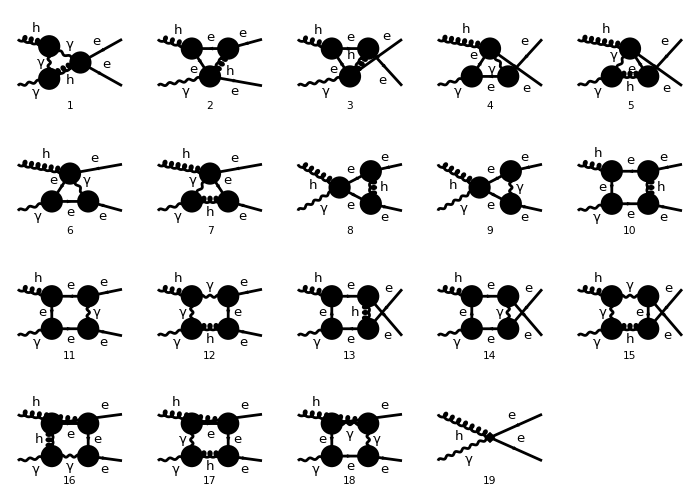

```mathematica
fields1={InsertionLevel->{Classes},GenericModel->FileNameJoin[{"Einstein_QED_2","Einstein_QED_2"}],Model->FileNameJoin[{"Einstein_QED_2","Einstein_QED_2"}]};
top1[i_,j_]:=CreateTopologies[1,i->j,ExcludeTopologies->{Reducible},Adjacencies->{3,4,5}];
top1CT[i_,j_]:=CreateCTTopologies[1,i->j,ExcludeTopologies->{Reducible},Adjacencies->{3,4,5}];
{hApsi1,hApsi1CT}=(InsertFields[#1,{T[1],V[1]}->{-F[1],F[1]},Sequence@@fields1]&)/@{top1[2,2],top1CT[2,2]};
diag4[0]=hApsi1[[0]][Sequence@@hApsi1,Sequence@@hApsi1CT];
Paint[diag4[0],ColumnsXRows->{5,4},SheetHeader->{""},Numbering->Simple,ImageSize->{700,500}];
```

We will only compute the diagrams proportional to κ. To compute the full contribution proportional to κ.b3, we would need to introduce terms proportional to κ.b2 in our action and this is beyond the scope of this work.

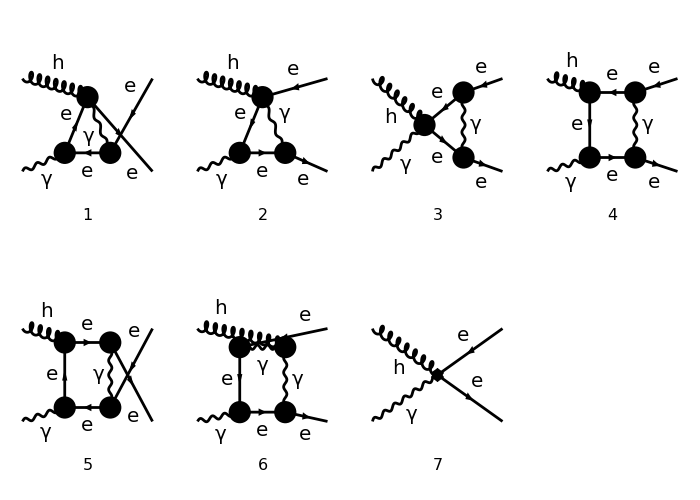

```mathematica
diag4[1]=DiagramDelete[diag4[0],{1,2,3,5,7,8,10,12,13,15,16,17}];
Paint[diag4[1],ColumnsXRows->{4,2},SheetHeader->{""},Numbering->Simple,ImageSize->{700,500}];
```

```mathematica
AbsoluteTiming[For[
i=1,i≤7,i++,{
amp[i]=DiagramExtract[diag4[1],i],
amp1[i]=FCFAConvert[CreateFeynAmp[amp[i],Truncated->True,PreFactor->1,GaugeRules->{}],IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},LoopMomenta->{k},List->False,SMP->True,ChangeDimension->D,LorentzIndexNames->{mu,nu,α,γ,δ,β,ξ,χ},UndoChiralSplittings->True,Contract->True,FinalSubstitutions->{Z4->1+δ4}]//Simplify,
amp2[i]=DiracSimplify[TID[amp1[i],k,ToPaVe->True,UsePaVeBasis->True]],
amp3[i]=SelectNotFree2[Normal[Series[FCReplaceD[PaVeUVPart[amp2[i],Prefactor->1/(2*π)^D],D->4-2*Epsilon],{Epsilon,0,0}]],{Epsilon,δ4}]}
];]
```

{2332.87,Null}

```mathematica
amp4=Sum[amp3[i],{i,1,7}]
```

(ⅈ κ (-ξ_(V(1)) γ^μ.γ^ν.γ^α+γ^μ.γ^ν.γ^α+2 γ^μ.γ^α.γ^ν+4 γ^α ξ_(V(1)) g^μν) e^3)/(128 ε π^2)+(ⅈ κ (2 γ^ν.γ^α.γ^μ+γ^α.γ^ν.γ^μ-γ^α.γ^ν.γ^μ ξ_(V(1))+4 γ^α ξ_(V(1)) g^μν) e^3)/(128 ε π^2)+(ⅈ κ ξ_(V(1)) (γ^α g^μν-γ^μ g^να) e^3)/(32 ε π^2)+1/2 ⅈ κ δ4 γ^α g^μν e-1/2 ⅈ κ δ4 γ^μ g^να e+(ⅈ (-3 κ γ^μ.γ^ν.γ^α e^3+6 κ γ^ν.γ^α.γ^μ e^3+3 κ γ^μ.γ^ν.γ^α ξ_(V(1)) e^3+8 κ γ^α g^μν e^3-12 κ γ^α ξ_(V(1)) g^μν e^3-4 κ γ^ν g^μα e^3-4 κ γ^μ g^να e^3))/(384 ε π^2)-(ⅈ (3 κ γ^μ.γ^ν.γ^α e^3+6 κ γ^μ.γ^α.γ^ν e^3+3 κ γ^ν.γ^μ.γ^α e^3+6 κ γ^ν.γ^α.γ^μ e^3+3 κ γ^α.γ^μ.γ^ν e^3+3 κ γ^α.γ^ν.γ^μ e^3-8 κ γ^α g^μν e^3+4 κ γ^ν g^μα e^3+4 κ γ^μ g^να e^3))/(384 ε π^2)+(ⅈ (6 κ γ^ν.γ^μ.γ^α e^3-3 κ γ^α.γ^ν.γ^μ e^3+3 κ γ^α.γ^ν.γ^μ ξ_(V(1)) e^3-4 κ γ^α g^μν e^3-12 κ γ^α ξ_(V(1)) g^μν e^3-4 κ γ^ν g^μα e^3+8 κ γ^μ g^να e^3))/(384 ε π^2)

Now, to simplify this expression, we use γ^μ γ^ν γ^ρ = η^{μν} γ^ρ + η^{νρ} γ^μ - η^{μρ} γ^ν - iϵ^{μνρσ} γ_σ γ⁵.

```mathematica
amp5=amp4/.{DiracGamma[LorentzIndex[mu,D],D].DiracGamma[LorentzIndex[α,D],D].DiracGamma[LorentzIndex[nu,D],D]->Pair[LorentzIndex[mu,D],LorentzIndex[α,D]]*DiracGamma[LorentzIndex[nu,D],D]+Pair[LorentzIndex[α,D],LorentzIndex[nu,D]]*DiracGamma[LorentzIndex[mu,D],D]-Pair[LorentzIndex[mu,D],LorentzIndex[nu,D]]*DiracGamma[LorentzIndex[α,D],D]-I*Eps[LorentzIndex[σ,D],LorentzIndex[mu,D],LorentzIndex[α,D],LorentzIndex[nu,D]]*DiracGamma[LorentzIndex[σ,D],D]*GA5,DiracGamma[LorentzIndex[mu,D],D].DiracGamma[LorentzIndex[nu,D],D].DiracGamma[LorentzIndex[α,D],D]->Pair[LorentzIndex[mu,D],LorentzIndex[nu,D]]*DiracGamma[LorentzIndex[α,D],D]+Pair[LorentzIndex[nu,D],LorentzIndex[α,D]]*DiracGamma[LorentzIndex[mu,D],D]-Pair[LorentzIndex[mu,D],LorentzIndex[α,D]]*DiracGamma[LorentzIndex[nu,D],D]-I*Eps[LorentzIndex[σ,D],LorentzIndex[mu,D],LorentzIndex[nu,D],LorentzIndex[α,D]]*DiracGamma[LorentzIndex[σ,D],D]*GA5,DiracGamma[LorentzIndex[nu,D],D].DiracGamma[LorentzIndex[mu,D],D].DiracGamma[LorentzIndex[α,D],D]->Pair[LorentzIndex[nu,D],LorentzIndex[mu,D]]*DiracGamma[LorentzIndex[α,D],D]+Pair[LorentzIndex[mu,D],LorentzIndex[α,D]]*DiracGamma[LorentzIndex[nu,D],D]-Pair[LorentzIndex[nu,D],LorentzIndex[α,D]]*DiracGamma[LorentzIndex[mu,D],D]-I*Eps[LorentzIndex[σ,D],LorentzIndex[nu,D],LorentzIndex[mu,D],LorentzIndex[α,D]]*DiracGamma[LorentzIndex[σ,D],D]*GA5,DiracGamma[LorentzIndex[nu,D],D].DiracGamma[LorentzIndex[α,D],D].DiracGamma[LorentzIndex[mu,D],D]->Pair[LorentzIndex[nu,D],LorentzIndex[α,D]]*DiracGamma[LorentzIndex[mu,D],D]+Pair[LorentzIndex[α,D],LorentzIndex[mu,D]]*DiracGamma[LorentzIndex[nu,D],D]-Pair[LorentzIndex[nu,D],LorentzIndex[mu,D]]*DiracGamma[LorentzIndex[α,D],D]-I*Eps[LorentzIndex[σ,D],LorentzIndex[nu,D],LorentzIndex[α,D],LorentzIndex[mu,D]]*DiracGamma[LorentzIndex[σ,D],D]*GA5,DiracGamma[LorentzIndex[α,D],D].DiracGamma[LorentzIndex[nu,D],D].DiracGamma[LorentzIndex[mu,D],D]->Pair[LorentzIndex[α,D],LorentzIndex[nu,D]]*DiracGamma[LorentzIndex[mu,D],D]+Pair[LorentzIndex[nu,D],LorentzIndex[mu,D]]*DiracGamma[LorentzIndex[α,D],D]-Pair[LorentzIndex[α,D],LorentzIndex[mu,D]]*DiracGamma[LorentzIndex[nu,D],D]-I*Eps[LorentzIndex[σ,D],LorentzIndex[α,D],LorentzIndex[nu,D],LorentzIndex[mu,D]]*DiracGamma[LorentzIndex[σ,D],D]*GA5,DiracGamma[LorentzIndex[α,D],D].DiracGamma[LorentzIndex[mu,D],D].DiracGamma[LorentzIndex[nu,D],D]->Pair[LorentzIndex[α,D],LorentzIndex[mu,D]]*DiracGamma[LorentzIndex[nu,D],D]+Pair[LorentzIndex[mu,D],LorentzIndex[nu,D]]*DiracGamma[LorentzIndex[α,D],D]-Pair[LorentzIndex[α,D],LorentzIndex[nu,D]]*DiracGamma[LorentzIndex[mu,D],D]-I*Eps[LorentzIndex[σ,D],LorentzIndex[α,D],LorentzIndex[mu,D],LorentzIndex[nu,D]]*DiracGamma[LorentzIndex[σ,D],D]*GA5}//Simplify
```

(e κ (e^2 (-(γ̄)^5) γ^σ ((ϵ^)^σμνα-(ϵ^)^σνμα-2 (ϵ^)^σναμ+(ϵ^)^σαμν+(ϵ^)^σανμ)+4 ⅈ γ^α g^μν (16 π^2 δ4 ε+e^2 ξ_(V(1)))-4 ⅈ γ^μ g^να (16 π^2 δ4 ε+e^2 ξ_(V(1)))))/(128 π^2 ε)

Finally, using the anticommutation property of the Levi-Civita symbol, we see that all the dependence in it vanishes and we can find δ4.

```mathematica
Flatten[Solve[SelectFree2[amp5,Eps]==0,δ4]]
```

{δ4→-(e^2 ξ_(V(1)))/(16 π^2 ε)}

#### 1-loop AAh

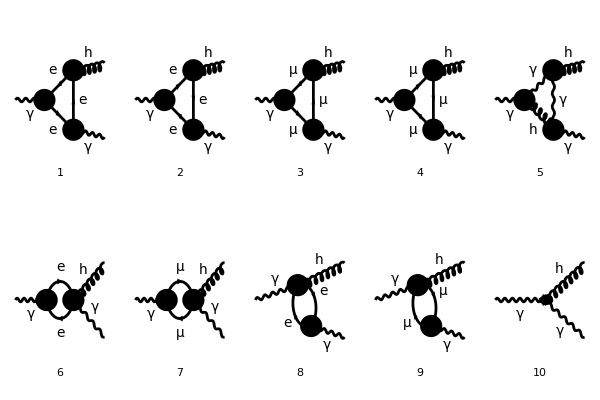

```mathematica
fields1={InsertionLevel->{Classes},GenericModel->FileNameJoin[{"Einstein_QED_2","Einstein_QED_2"}],Model->FileNameJoin[{"Einstein_QED_2","Einstein_QED_2"}]};
top1[i_,j_]:=CreateTopologies[1,i->j,ExcludeTopologies->{Reducible},Adjacencies->{3,4,5}];
top1CT[i_,j_]:=CreateCTTopologies[1,i->j,ExcludeTopologies->{Reducible},Adjacencies->{3,4,5}];
{hA1,hA1CT}=(InsertFields[#1,{V[1]}->{T[1],V[1]},Sequence@@fields1]&)/@{top1[1,2],top1CT[1,2]};
diag5[0]=hA1[[0]][Sequence@@hA1,Sequence@@hA1CT];
Paint[diag5[0],ColumnsXRows->{5,2},SheetHeader->{""},Numbering->Simple,ImageSize->{600,400}];
```

```mathematica
AbsoluteTiming[For[
i=1,i≤10,i++,{
amp[i]=DiagramExtract[diag5[0],i],
amp1[i]=FCFAConvert[CreateFeynAmp[amp[i],Truncated->True,PreFactor->1,GaugeRules->{}],IncomingMomenta->{p1},OutgoingMomenta->{p2,p3},LoopMomenta->{k},List->False,SMP->True,ChangeDimension->D,LorentzIndexNames->{mu,nu,α,γ,δ,β,ξ,χ},UndoChiralSplittings->True,Contract->True,FinalSubstitutions->{Z6->1+δ6}]//Simplify,
amp2[i]=DiracSimplify[TID[amp1[i],k,ToPaVe->True,UsePaVeBasis->True]],
amp3[i]=SelectNotFree2[Normal[Series[FCReplaceD[PaVeUVPart[amp2[i],Prefactor->1/(2*π)^D],D->4-2*Epsilon],{Epsilon,0,0}]],{Epsilon,δ6}]}
];]
```

{344.413,Null}

```mathematica
amp1[10]
```

1/2 ⅈ δ6 κ (p_1^γ p_3^ν (-g^μα)-p_1^γ p_3^α g^μν-p_3^μ (p_1^ν g^αγ+p_1^α g^νγ-p_1^γ g^να)+g^μα g^νγ (p_1·p_3)+g^αγ g^μν (p_1·p_3)+g^μγ (-g^να (p_1·p_3)+p_1^α p_3^ν+p_1^ν p_3^α))

```mathematica
amp4=Collect2[Sum[amp3[i],{i,1,9}]+amp1[10],{Pair[Momentum[p2,D],LorentzIndex[mu,D]],Pair[Momentum[p2,D],LorentzIndex[nu,D]],Pair[Momentum[p2,D],LorentzIndex[α,D]],δ6}]
```

(ⅈ p_2^ν p_2^α (p_3^μ p_1^γ-g^μγ (p_1·p_3)) κ^3)/(192 ε π^2)+(ⅈ (4 ξ_(T(1))-3) p_2^μ p_2^α (p_3^ν p_1^γ-g^νγ (p_1·p_3)) κ^3)/(384 ε π^2)+(ⅈ (4 ξ_(T(1))-3) p_2^μ p_2^ν (p_3^α p_1^γ-g^αγ (p_1·p_3)) κ^3)/(384 ε π^2)-1/(768 ε π^2)ⅈ p_2^μ (8 ξ_(T(1)) p_3^ν p_3^α p_1^γ-2 p_3^ν p_3^α p_1^γ+4 ξ_(T(1)) g^να (p_2·p_3) p_1^γ-2 g^να (p_2·p_3) p_1^γ-12 ξ_(T(1)) g^να p_3^2 p_1^γ+7 g^να p_3^2 p_1^γ-8 ξ_(T(1)) p_3^ν p_1^α p_3^γ+4 p_3^ν p_1^α p_3^γ-8 ξ_(T(1)) p_1^ν p_3^α p_3^γ+4 p_1^ν p_3^α p_3^γ-4 ξ_(T(1)) p_3^ν g^αγ (p_1·p_3)+p_3^ν g^αγ (p_1·p_3)-4 ξ_(T(1)) g^νγ p_3^α (p_1·p_3)+g^νγ p_3^α (p_1·p_3)-4 ξ_(T(1)) g^να p_2^γ (p_1·p_3)+2 g^να p_2^γ (p_1·p_3)+12 ξ_(T(1)) g^να p_3^γ (p_1·p_3)-7 g^να p_3^γ (p_1·p_3)+8 ξ_(T(1)) p_1^ν g^αγ p_3^2-4 p_1^ν g^αγ p_3^2+8 ξ_(T(1)) g^νγ p_1^α p_3^2-4 g^νγ p_1^α p_3^2) κ^3-1/2 ⅈ δ6 (p_3^μ p_1^ν g^αγ-g^μν (p_1·p_3) g^αγ+p_3^μ g^νγ p_1^α-g^μγ p_3^ν p_1^α-g^μγ p_1^ν p_3^α-p_3^μ g^να p_1^γ+g^μα p_3^ν p_1^γ+g^μν p_3^α p_1^γ+g^μγ g^να (p_1·p_3)-g^μα g^νγ (p_1·p_3)) κ+1/(768 ε π^2)ⅈ p_2^α (20 ξ_(T(1)) p_3^μ p_3^ν p_1^γ κ^2-9 p_3^μ p_3^ν p_1^γ κ^2+2 p_3^μ p_1^ν p_2^γ κ^2-12 ξ_(T(1)) p_3^μ p_1^ν p_3^γ κ^2+9 p_3^μ p_1^ν p_3^γ κ^2+8 ξ_(T(1)) p_3^μ g^νγ (p_1·p_2) κ^2-6 p_3^μ g^νγ (p_1·p_2) κ^2-8 ξ_(T(1)) g^μγ p_3^ν (p_1·p_2) κ^2+6 g^μγ p_3^ν (p_1·p_2) κ^2-20 ξ_(T(1)) g^μγ p_3^ν (p_1·p_3) κ^2+9 g^μγ p_3^ν (p_1·p_3) κ^2-2 g^μν p_2^γ (p_1·p_3) κ^2+12 ξ_(T(1)) g^μν p_3^γ (p_1·p_3) κ^2-9 g^μν p_3^γ (p_1·p_3) κ^2-2 g^μγ p_1^ν (p_2·p_3) κ^2+2 g^μν p_1^γ (p_2·p_3) κ^2+12 ξ_(T(1)) g^μγ p_1^ν p_3^2 κ^2-9 g^μγ p_1^ν p_3^2 κ^2-12 ξ_(T(1)) g^μν p_1^γ p_3^2 κ^2+9 g^μν p_1^γ p_3^2 κ^2-64 p_3^μ g^νγ e^2+64 g^μγ p_3^ν e^2) κ+1/(768 ε π^2)ⅈ p_2^ν (20 ξ_(T(1)) p_3^μ p_3^α p_1^γ κ^2-9 p_3^μ p_3^α p_1^γ κ^2+2 p_3^μ p_1^α p_2^γ κ^2-12 ξ_(T(1)) p_3^μ p_1^α p_3^γ κ^2+9 p_3^μ p_1^α p_3^γ κ^2+8 ξ_(T(1)) p_3^μ g^αγ (p_1·p_2) κ^2-6 p_3^μ g^αγ (p_1·p_2) κ^2-8 ξ_(T(1)) g^μγ p_3^α (p_1·p_2) κ^2+6 g^μγ p_3^α (p_1·p_2) κ^2-20 ξ_(T(1)) g^μγ p_3^α (p_1·p_3) κ^2+9 g^μγ p_3^α (p_1·p_3) κ^2-2 g^μα p_2^γ (p_1·p_3) κ^2+12 ξ_(T(1)) g^μα p_3^γ (p_1·p_3) κ^2-9 g^μα p_3^γ (p_1·p_3) κ^2-2 g^μγ p_1^α (p_2·p_3) κ^2+2 g^μα p_1^γ (p_2·p_3) κ^2+12 ξ_(T(1)) g^μγ p_1^α p_3^2 κ^2-9 g^μγ p_1^α p_3^2 κ^2-12 ξ_(T(1)) g^μα p_1^γ p_3^2 κ^2+9 g^μα p_1^γ p_3^2 κ^2-64 p_3^μ g^αγ e^2+64 g^μγ p_3^α e^2) κ+1/(768 ε π^2)ⅈ (16 ξ_(T(1)) p_3^μ p_3^ν p_3^α p_1^γ κ^2-12 ξ_(T(1)) p_3^μ p_3^ν p_1^α p_2^γ κ^2+9 p_3^μ p_3^ν p_1^α p_2^γ κ^2-12 ξ_(T(1)) p_3^μ p_1^ν p_3^α p_2^γ κ^2+9 p_3^μ p_1^ν p_3^α p_2^γ κ^2-8 ξ_(T(1)) p_3^μ p_3^ν p_1^α p_3^γ κ^2+6 p_3^μ p_3^ν p_1^α p_3^γ κ^2-8 ξ_(T(1)) p_3^μ p_1^ν p_3^α p_3^γ κ^2+6 p_3^μ p_1^ν p_3^α p_3^γ κ^2-4 ξ_(T(1)) p_3^μ p_3^ν g^αγ (p_1·p_2) κ^2+p_3^μ p_3^ν g^αγ (p_1·p_2) κ^2-4 ξ_(T(1)) p_3^μ g^νγ p_3^α (p_1·p_2) κ^2+p_3^μ g^νγ p_3^α (p_1·p_2) κ^2+8 ξ_(T(1)) g^μγ p_3^ν p_3^α (p_1·p_2) κ^2-2 g^μγ p_3^ν p_3^α (p_1·p_2) κ^2-4 ξ_(T(1)) p_3^μ g^να p_2^γ (p_1·p_2) κ^2+2 p_3^μ g^να p_2^γ (p_1·p_2) κ^2+12 ξ_(T(1)) p_3^μ g^να p_3^γ (p_1·p_2) κ^2-7 p_3^μ g^να p_3^γ (p_1·p_2) κ^2-8 ξ_(T(1)) g^μα p_3^ν p_3^γ (p_1·p_2) κ^2+4 g^μα p_3^ν p_3^γ (p_1·p_2) κ^2-8 ξ_(T(1)) g^μν p_3^α p_3^γ (p_1·p_2) κ^2+4 g^μν p_3^α p_3^γ (p_1·p_2) κ^2-16 ξ_(T(1)) g^μγ p_3^ν p_3^α (p_1·p_3) κ^2+12 ξ_(T(1)) g^μα p_3^ν p_2^γ (p_1·p_3) κ^2-9 g^μα p_3^ν p_2^γ (p_1·p_3) κ^2+12 ξ_(T(1)) g^μν p_3^α p_2^γ (p_1·p_3) κ^2-9 g^μν p_3^α p_2^γ (p_1·p_3) κ^2+8 ξ_(T(1)) g^μα p_3^ν p_3^γ (p_1·p_3) κ^2-6 g^μα p_3^ν p_3^γ (p_1·p_3) κ^2+8 ξ_(T(1)) g^μν p_3^α p_3^γ (p_1·p_3) κ^2-6 g^μν p_3^α p_3^γ (p_1·p_3) κ^2-8 ξ_(T(1)) p_3^μ p_1^ν g^αγ p_2^2 κ^2+5 p_3^μ p_1^ν g^αγ p_2^2 κ^2-8 ξ_(T(1)) p_3^μ g^νγ p_1^α p_2^2 κ^2+5 p_3^μ g^νγ p_1^α p_2^2 κ^2+8 ξ_(T(1)) g^μγ p_3^ν p_1^α p_2^2 κ^2-5 g^μγ p_3^ν p_1^α p_2^2 κ^2+8 ξ_(T(1)) g^μγ p_1^ν p_3^α p_2^2 κ^2-5 g^μγ p_1^ν p_3^α p_2^2 κ^2+8 ξ_(T(1)) p_3^μ g^να p_1^γ p_2^2 κ^2-6 p_3^μ g^να p_1^γ p_2^2 κ^2-8 ξ_(T(1)) g^μα p_3^ν p_1^γ p_2^2 κ^2+5 g^μα p_3^ν p_1^γ p_2^2 κ^2-8 ξ_(T(1)) g^μν p_3^α p_1^γ p_2^2 κ^2+5 g^μν p_3^α p_1^γ p_2^2 κ^2-8 ξ_(T(1)) g^μγ g^να (p_1·p_3) p_2^2 κ^2+6 g^μγ g^να (p_1·p_3) p_2^2 κ^2+8 ξ_(T(1)) g^μα g^νγ (p_1·p_3) p_2^2 κ^2-5 g^μα g^νγ (p_1·p_3) p_2^2 κ^2+8 ξ_(T(1)) g^μν g^αγ (p_1·p_3) p_2^2 κ^2-5 g^μν g^αγ (p_1·p_3) p_2^2 κ^2+8 ξ_(T(1)) p_3^μ p_1^ν g^αγ (p_2·p_3) κ^2-3 p_3^μ p_1^ν g^αγ (p_2·p_3) κ^2+8 ξ_(T(1)) p_3^μ g^νγ p_1^α (p_2·p_3) κ^2-3 p_3^μ g^νγ p_1^α (p_2·p_3) κ^2+4 ξ_(T(1)) g^μγ p_3^ν p_1^α (p_2·p_3) κ^2-6 g^μγ p_3^ν p_1^α (p_2·p_3) κ^2+4 ξ_(T(1)) g^μγ p_1^ν p_3^α (p_2·p_3) κ^2-6 g^μγ p_1^ν p_3^α (p_2·p_3) κ^2-12 ξ_(T(1)) p_3^μ g^να p_1^γ (p_2·p_3) κ^2+3 p_3^μ g^να p_1^γ (p_2·p_3) κ^2-4 ξ_(T(1)) g^μα p_3^ν p_1^γ (p_2·p_3) κ^2+6 g^μα p_3^ν p_1^γ (p_2·p_3) κ^2-4 ξ_(T(1)) g^μν p_3^α p_1^γ (p_2·p_3) κ^2+6 g^μν p_3^α p_1^γ (p_2·p_3) κ^2+4 ξ_(T(1)) g^μγ g^να (p_1·p_2) (p_2·p_3) κ^2-2 g^μγ g^να (p_1·p_2) (p_2·p_3) κ^2+12 ξ_(T(1)) g^μγ g^να (p_1·p_3) (p_2·p_3) κ^2-3 g^μγ g^να (p_1·p_3) (p_2·p_3) κ^2-8 ξ_(T(1)) g^μα g^νγ (p_1·p_3) (p_2·p_3) κ^2+3 g^μα g^νγ (p_1·p_3) (p_2·p_3) κ^2-8 ξ_(T(1)) g^μν g^αγ (p_1·p_3) (p_2·p_3) κ^2+3 g^μν g^αγ (p_1·p_3) (p_2·p_3) κ^2+p_3^μ p_1^ν g^αγ p_3^2 κ^2+p_3^μ g^νγ p_1^α p_3^2 κ^2+8 ξ_(T(1)) g^μγ p_3^ν p_1^α p_3^2 κ^2-7 g^μγ p_3^ν p_1^α p_3^2 κ^2+8 ξ_(T(1)) g^μγ p_1^ν p_3^α p_3^2 κ^2-7 g^μγ p_1^ν p_3^α p_3^2 κ^2-4 p_3^μ g^να p_1^γ p_3^2 κ^2-8 ξ_(T(1)) g^μα p_3^ν p_1^γ p_3^2 κ^2+7 g^μα p_3^ν p_1^γ p_3^2 κ^2-8 ξ_(T(1)) g^μν p_3^α p_1^γ p_3^2 κ^2+7 g^μν p_3^α p_1^γ p_3^2 κ^2-12 ξ_(T(1)) g^μγ g^να (p_1·p_2) p_3^2 κ^2+7 g^μγ g^να (p_1·p_2) p_3^2 κ^2+8 ξ_(T(1)) g^μα g^νγ (p_1·p_2) p_3^2 κ^2-4 g^μα g^νγ (p_1·p_2) p_3^2 κ^2+8 ξ_(T(1)) g^μν g^αγ (p_1·p_2) p_3^2 κ^2-4 g^μν g^αγ (p_1·p_2) p_3^2 κ^2+4 g^μγ g^να (p_1·p_3) p_3^2 κ^2-g^μα g^νγ (p_1·p_3) p_3^2 κ^2-g^μν g^αγ (p_1·p_3) p_3^2 κ^2-64 p_3^μ p_3^ν g^αγ e^2-64 p_3^μ g^νγ p_3^α e^2+128 g^μγ p_3^ν p_3^α e^2+64 p_3^μ g^να p_2^γ e^2-64 g^μα p_3^ν p_2^γ e^2-64 g^μν p_3^α p_2^γ e^2+64 p_3^μ g^να p_3^γ e^2-64 g^μα p_3^ν p_3^γ e^2-64 g^μν p_3^α p_3^γ e^2-64 g^μγ g^να (p_2·p_3) e^2+64 g^μα g^νγ (p_2·p_3) e^2+64 g^μν g^αγ (p_2·p_3) e^2-64 g^μγ g^να p_3^2 e^2+64 g^μα g^νγ p_3^2 e^2+64 g^μν g^αγ p_3^2 e^2) κ

Since we are only interested in the renormalization of δ6, discard the terms that will be renormalized by the HO counterterms

```mathematica
amp5=Collect2[SelectFree2[amp4,{Pair[Momentum[p3,D],LorentzIndex[nu,D]]*Pair[Momentum[p3,D],LorentzIndex[α,D]]*Pair[Momentum[p1,D],LorentzIndex[γ,D]],Pair[Momentum[p2,D], Momentum[p3,D]]*Pair[Momentum[p1,D],LorentzIndex[γ,D]],Pair[Momentum[p3,D], Momentum[p3,D]]*Pair[Momentum[p1,D],LorentzIndex[γ,D]],Pair[Momentum[p3,D],LorentzIndex[nu,D]]*Pair[Momentum[p1,D],LorentzIndex[α,D]]*Pair[Momentum[p3,D],LorentzIndex[γ,D]],Pair[Momentum[p1,D],LorentzIndex[nu,D]]*Pair[Momentum[p3,D],LorentzIndex[α,D]]*Pair[Momentum[p3,D],LorentzIndex[γ,D]],Pair[Momentum[p1,D], Momentum[p3,D]]*Pair[Momentum[p3,D],LorentzIndex[nu,D]],Pair[Momentum[p1,D], Momentum[p3,D]]*Pair[Momentum[p3,D],LorentzIndex[α,D]],Pair[Momentum[p1,D], Momentum[p3,D]]*Pair[Momentum[p2,D],LorentzIndex[γ,D]],Pair[Momentum[p1,D],Momentum[p2,D]]}],{Momentum[p1,D],Z6}]
```

-1/(12 ε π^2)ⅈ κ (p_3^μ p_2^ν g^αγ+p_3^μ p_3^ν g^αγ-g^μν (p_2·p_3) g^αγ-g^μν p_3^2 g^αγ+p_3^μ g^νγ p_2^α-g^μγ p_3^ν p_2^α+p_3^μ g^νγ p_3^α-g^μγ p_2^ν p_3^α-2 g^μγ p_3^ν p_3^α-p_3^μ g^να p_2^γ+g^μα p_3^ν p_2^γ+g^μν p_3^α p_2^γ-p_3^μ g^να p_3^γ+g^μα p_3^ν p_3^γ+g^μν p_3^α p_3^γ+g^μγ g^να (p_2·p_3)-g^μα g^νγ (p_2·p_3)+g^μγ g^να p_3^2-g^μα g^νγ p_3^2) e^2+1/(768 ε π^2)ⅈ κ p_1^γ (4 p_3^μ p_2^ν p_2^α κ^2+8 ξ_(T(1)) p_2^μ p_3^ν p_2^α κ^2-6 p_2^μ p_3^ν p_2^α κ^2+20 ξ_(T(1)) p_3^μ p_3^ν p_2^α κ^2-9 p_3^μ p_3^ν p_2^α κ^2+8 ξ_(T(1)) p_2^μ p_2^ν p_3^α κ^2-6 p_2^μ p_2^ν p_3^α κ^2+20 ξ_(T(1)) p_3^μ p_2^ν p_3^α κ^2-9 p_3^μ p_2^ν p_3^α κ^2+8 ξ_(T(1)) p_3^μ g^να p_2^2 κ^2-6 p_3^μ g^να p_2^2 κ^2-8 ξ_(T(1)) g^μα p_3^ν p_2^2 κ^2+5 g^μα p_3^ν p_2^2 κ^2-8 ξ_(T(1)) g^μν p_3^α p_2^2 κ^2+5 g^μν p_3^α p_2^2 κ^2+384 ε π^2 δ6 p_3^μ g^να-384 ε π^2 δ6 g^μα p_3^ν-384 ε π^2 δ6 g^μν p_3^α)-1/(768 ε π^2)ⅈ κ p_1^α (-2 p_3^μ p_2^ν p_2^γ κ^2+12 ξ_(T(1)) p_3^μ p_3^ν p_2^γ κ^2-9 p_3^μ p_3^ν p_2^γ κ^2+12 ξ_(T(1)) p_3^μ p_2^ν p_3^γ κ^2-9 p_3^μ p_2^ν p_3^γ κ^2+8 ξ_(T(1)) p_3^μ g^νγ p_2^2 κ^2-5 p_3^μ g^νγ p_2^2 κ^2-8 ξ_(T(1)) g^μγ p_3^ν p_2^2 κ^2+5 g^μγ p_3^ν p_2^2 κ^2-8 ξ_(T(1)) p_3^μ g^νγ (p_2·p_3) κ^2+3 p_3^μ g^νγ (p_2·p_3) κ^2+2 g^μγ p_2^ν (p_2·p_3) κ^2-4 ξ_(T(1)) g^μγ p_3^ν (p_2·p_3) κ^2+6 g^μγ p_3^ν (p_2·p_3) κ^2+8 ξ_(T(1)) p_2^μ g^νγ p_3^2 κ^2-4 p_2^μ g^νγ p_3^2 κ^2-p_3^μ g^νγ p_3^2 κ^2-12 ξ_(T(1)) g^μγ p_2^ν p_3^2 κ^2+9 g^μγ p_2^ν p_3^2 κ^2-8 ξ_(T(1)) g^μγ p_3^ν p_3^2 κ^2+7 g^μγ p_3^ν p_3^2 κ^2+384 ε π^2 δ6 p_3^μ g^νγ-384 ε π^2 δ6 g^μγ p_3^ν)-1/(768 ε π^2)ⅈ κ (p_1·p_3) (8 ξ_(T(1)) p_2^μ p_2^ν g^αγ κ^2-6 p_2^μ p_2^ν g^αγ κ^2+8 ξ_(T(1)) p_2^μ g^νγ p_2^α κ^2-6 p_2^μ g^νγ p_2^α κ^2+4 g^μγ p_2^ν p_2^α κ^2+12 ξ_(T(1)) p_2^μ g^να p_3^γ κ^2-7 p_2^μ g^να p_3^γ κ^2-12 ξ_(T(1)) g^μα p_2^ν p_3^γ κ^2+9 g^μα p_2^ν p_3^γ κ^2-12 ξ_(T(1)) g^μν p_2^α p_3^γ κ^2+9 g^μν p_2^α p_3^γ κ^2+8 ξ_(T(1)) g^μγ g^να p_2^2 κ^2-6 g^μγ g^να p_2^2 κ^2-8 ξ_(T(1)) g^μα g^νγ p_2^2 κ^2+5 g^μα g^νγ p_2^2 κ^2-8 ξ_(T(1)) g^μν g^αγ p_2^2 κ^2+5 g^μν g^αγ p_2^2 κ^2-12 ξ_(T(1)) g^μγ g^να (p_2·p_3) κ^2+3 g^μγ g^να (p_2·p_3) κ^2+8 ξ_(T(1)) g^μα g^νγ (p_2·p_3) κ^2-3 g^μα g^νγ (p_2·p_3) κ^2+8 ξ_(T(1)) g^μν g^αγ (p_2·p_3) κ^2-3 g^μν g^αγ (p_2·p_3) κ^2-4 g^μγ g^να p_3^2 κ^2+g^μα g^νγ p_3^2 κ^2+g^μν g^αγ p_3^2 κ^2+384 ε π^2 δ6 g^μγ g^να-384 ε π^2 δ6 g^μα g^νγ-384 ε π^2 δ6 g^μν g^αγ)-1/(768 ε π^2)ⅈ κ p_1^ν (-2 p_3^μ p_2^α p_2^γ κ^2+12 ξ_(T(1)) p_3^μ p_3^α p_2^γ κ^2-9 p_3^μ p_3^α p_2^γ κ^2+12 ξ_(T(1)) p_3^μ p_2^α p_3^γ κ^2-9 p_3^μ p_2^α p_3^γ κ^2+8 ξ_(T(1)) p_3^μ g^αγ p_2^2 κ^2-5 p_3^μ g^αγ p_2^2 κ^2-8 ξ_(T(1)) g^μγ p_3^α p_2^2 κ^2+5 g^μγ p_3^α p_2^2 κ^2-8 ξ_(T(1)) p_3^μ g^αγ (p_2·p_3) κ^2+3 p_3^μ g^αγ (p_2·p_3) κ^2+2 g^μγ p_2^α (p_2·p_3) κ^2-4 ξ_(T(1)) g^μγ p_3^α (p_2·p_3) κ^2+6 g^μγ p_3^α (p_2·p_3) κ^2+8 ξ_(T(1)) p_2^μ g^αγ p_3^2 κ^2-4 p_2^μ g^αγ p_3^2 κ^2-p_3^μ g^αγ p_3^2 κ^2-12 ξ_(T(1)) g^μγ p_2^α p_3^2 κ^2+9 g^μγ p_2^α p_3^2 κ^2-8 ξ_(T(1)) g^μγ p_3^α p_3^2 κ^2+7 g^μγ p_3^α p_3^2 κ^2+384 ε π^2 δ6 p_3^μ g^αγ-384 ε π^2 δ6 g^μγ p_3^α)

```mathematica
amp6=SelectFree2[amp5,Momentum[p1,D]]+SelectNotFree2[amp5,δ6]
```

-1/(12 π^2 ε)ⅈ e^2 κ (p_2^ν p_3^μ g^αγ+p_2^α p_3^μ g^νγ-p_2^α p_3^ν g^μγ-p_2^ν p_3^α g^μγ-p_2^γ p_3^μ g^να+p_2^γ p_3^ν g^μα+p_2^γ p_3^α g^μν-g^αγ g^μν (p_2·p_3)+g^να g^μγ (p_2·p_3)-g^μα g^νγ (p_2·p_3)+p_3^μ p_3^ν g^αγ-p_3^2 g^αγ g^μν+p_3^α p_3^μ g^νγ-2 p_3^α p_3^ν g^μγ-p_3^γ p_3^μ g^να+p_3^γ p_3^ν g^μα+p_3^α p_3^γ g^μν+p_3^2 g^να g^μγ-p_3^2 g^μα g^νγ)-1/2 ⅈ δ6 κ p_1^ν p_3^μ g^αγ-1/2 ⅈ δ6 κ p_1^α p_3^μ g^νγ+1/2 ⅈ δ6 κ p_1^α p_3^ν g^μγ+1/2 ⅈ δ6 κ p_1^ν p_3^α g^μγ+1/2 ⅈ δ6 κ p_1^γ p_3^μ g^να-1/2 ⅈ δ6 κ p_1^γ p_3^ν g^μα-1/2 ⅈ δ6 κ p_1^γ p_3^α g^μν-1/2 ⅈ δ6 κ g^να g^μγ (p_1·p_3)+1/2 ⅈ δ6 κ g^μα g^νγ (p_1·p_3)+1/2 ⅈ δ6 κ g^αγ g^μν (p_1·p_3)

Using p1=p2+p3

```mathematica
amp7=amp6/.{Pair[Momentum[p1,D],LorentzIndex[α,D]]->Pair[Momentum[p2,D],LorentzIndex[α,D]]+Pair[Momentum[p3,D],LorentzIndex[α,D]],Pair[Momentum[p1,D],LorentzIndex[nu,D]]->Pair[Momentum[p2,D],LorentzIndex[nu,D]]+Pair[Momentum[p3,D],LorentzIndex[nu,D]],Pair[Momentum[p1,D],LorentzIndex[γ,D]]->Pair[Momentum[p2,D],LorentzIndex[γ,D]]+Pair[Momentum[p3,D],LorentzIndex[γ,D]],Pair[Momentum[p1,D],Momentum[p3,D]]->Pair[Momentum[p2,D],Momentum[p3,D]]+Pair[Momentum[p3,D],Momentum[p3,D]]}//Expand//Simplify
```

-1/(12 π^2 ε)ⅈ κ (6 π^2 δ6 ε+e^2) (p_2^γ p_3^ν g^μα+p_2^γ p_3^α g^μν+p_3^μ (p_2^ν g^αγ+p_2^α g^νγ-p_2^γ g^να+p_3^ν g^αγ+p_3^α g^νγ-p_3^γ g^να)-g^μα g^νγ (p_2·p_3)-g^αγ g^μν (p_2·p_3)+g^μγ (g^να (p_2·p_3+p_3^2)-p_2^ν p_3^α-p_3^ν (p_2^α+2 p_3^α))+p_3^γ p_3^ν g^μα+p_3^α p_3^γ g^μν-p_3^2 g^μα g^νγ-p_3^2 g^αγ g^μν)

```mathematica
Solve[amp7==0,δ6]
```

{{δ6→-e^2/(6 π^2 ε)}}